```mathematica
MyFirst[list_]:=If[Length[list]>0,First[First[list]],0]
```

```mathematica
BadTail[max_]:=Module[{pow3,runLength,  x, valueTail, allTwos, result={},hold},
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=PadLeft[IntegerDigits[Mod[2^x,pow3],3],max+1];
If [!MemberQ[valueTail,2],
hold=Reverse[IntegerDigits[2^x,3]];
AppendTo[result,{x,MyFirst[ Position[hold,2]], Length[hold], valueTail}];
]
],
{x, runLength}];
result
]
```

```mathematica
TableForm[
Table[
Map[FromDigits[#[[4]],2]&,BadTail[i]],
{i,0,6}
],
TableDepth->1
]
```

{1}
{1,3}
{1,3,5,7}
{1,3,7,9,11,5,15,13}
{1,3,7,11,5,15,17,19,23,9,27,21,31,13,25,29}
{1,3,39,43,5,15,19,55,41,59,31,25,61,33,35,37,47,17,51,21,63,13,57,7,11,49,23,9,27,53,45,29}
{1,3,39,107,69,79,83,105,31,25,35,37,111,81,115,21,63,71,49,23,9,27,109,93,65,67,103,55,59,95,89,61,33,99,101,85,127,13,57,11,113,87,73,91,53,43,5,15,19,119,41,123,125,97,47,17,51,77,121,7,75,117,45,29}

```mathematica
TableForm[Take[
Sort[BadTail[14],#1[[2]]>#2[[2]]&], 20], TableDepth->2]
```

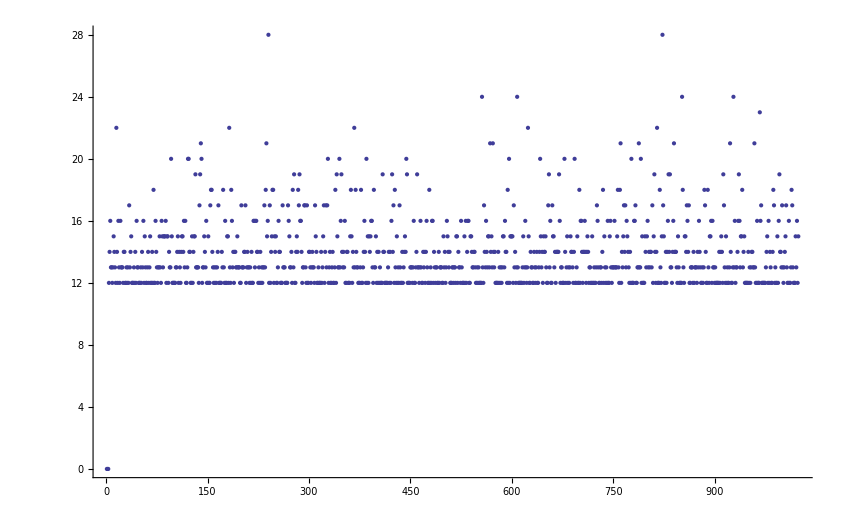

```mathematica
ListPlot[Map[#[[2]]&,BadTail[10]]]
```

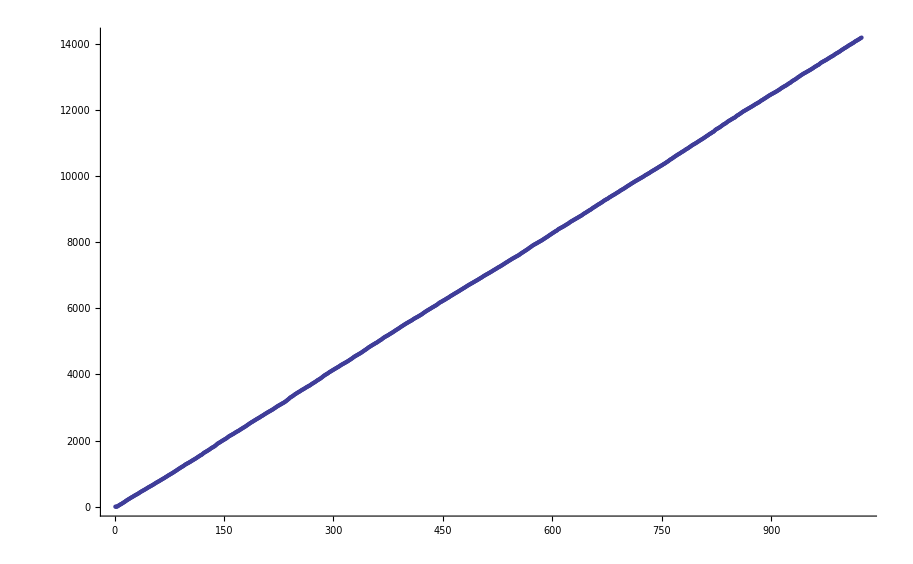

```mathematica
ListPlot[Accumulate[Map[#[[2]]&,BadTail[10]]]]
```

```mathematica
N[10*Log[2,3]]
```

15.8496

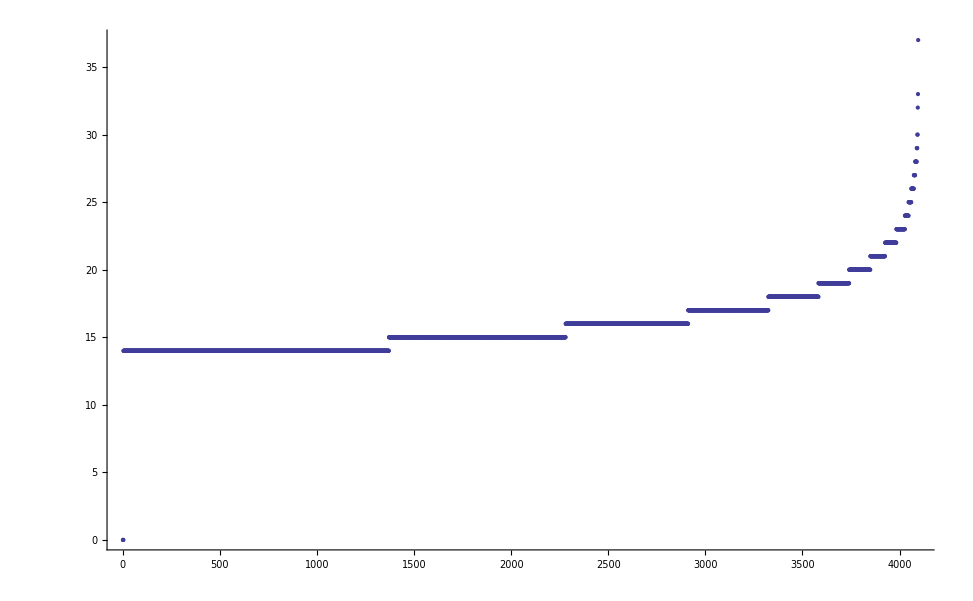

```mathematica
ListPlot[Sort[Map[#[[2]]&,BadTail[12]]], PlotRange->All]
```

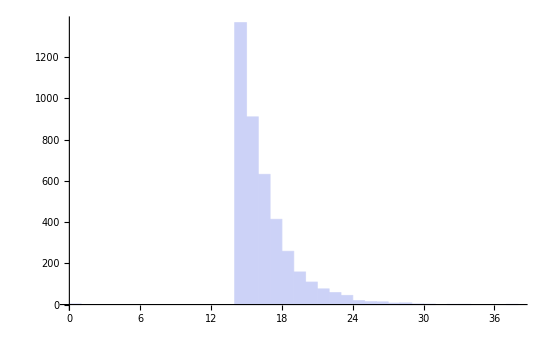

```mathematica
Histogram[Map[#[[2]]&,BadTail[12]]]
```

```mathematica
Sort[Map[{#[[1]],#[[2]]}&,BadTail[6]],#1[[2]]>#2[[2]]&]
```

{{1134,22},{332,16},{864,15},{1260,14},{992,14},{186,14},{1044,13},{774,13},{560,13},{474,13},{1046,12},{728,12},{72,12},{1190,11},{1028,11},{872,11},{242,11},{240,11},{126,11},{26,11},{24,11},{1392,10},{1374,10},{1230,10},{650,10},{566,10},{488,10},{386,10},{218,10},{188,10},{80,10},{1188,9},{1160,9},{882,9},{648,9},{636,9},{494,9},{378,9},{164,9},{1446,8},{1316,8},{1304,8},{1122,8},{1034,8},{998,8},{996,8},{888,8},{884,8},{830,8},{744,8},{726,8},{672,8},{612,8},{548,8},{486,8},{420,8},{398,8},{396,8},{216,8},{56,8},{20,8},{8,0},{2,0},{0,0}}

```mathematica
FromDigits[Take[IntegerDigits[2^1134,3],21],2]
```

2213813

```mathematica
TableForm [
Table[
Module[
{bt=Sort[BadTail[tailLength],#1[[2]]>#2[[2]]&], highest},
highest = First[bt][[2]];
Select[bt, #[[2]]==highest&]
],
{tailLength,1,12}
],
TableDepth->2
]
```

{2,0,2,{1,1}} | {0,0,1,{0,1}}
{6,4,4,{1,0,1}} | 
{26,11,17,{1,1,1,1}} | {24,11,16,{0,1,0,1}}
{72,12,46,{0,1,0,0,1}} | 
{332,16,210,{0,0,0,1,1,1}} | 
{1134,22,716,{1,1,0,0,0,0,1}} | 
{1134,22,716,{0,1,1,0,0,0,0,1}} | 
{1134,22,716,{1,0,1,1,0,0,0,0,1}} | 
{25458,28,16063,{0,1,1,1,1,0,0,1,0,1}} | 
{93246,28,58832,{1,0,1,1,0,1,0,1,1,0,1}} | {25458,28,16063,{1,0,1,1,1,1,0,0,1,0,1}}
{249968,37,157713,{0,1,0,0,1,1,1,0,0,0,1,1}} | 
{249968,37,157713,{1,0,1,0,0,1,1,1,0,0,0,1,1}} |

```mathematica
TableForm [
Table[
Module[
{bt=Sort[BadTail[tailLength],#1[[2]]>#2[[2]]&], highest},
highest = First[bt][[2]];
Select[bt, #[[2]]==highest&]
],
{tailLength,13,13}
],
TableDepth->2
]
```

{249968,37,157713,{0,1,0,1,0,0,1,1,1,0,0,0,1,1}}

```mathematica
TableForm [
Table[
Module[
{bt=Sort[BadTail[tailLength],#1[[2]]>#2[[2]]&], highest},
highest = First[bt][[2]];
Select[bt, #[[2]]==highest&]
],
{tailLength,14,14}
],
TableDepth->2
]
```

```mathematica
values={2,6,26,72,332,1134,1134,1134,25458, 93246, 249968}
```

{2,6,26,72,332,1134,1134,1134,25458,93246,249968}

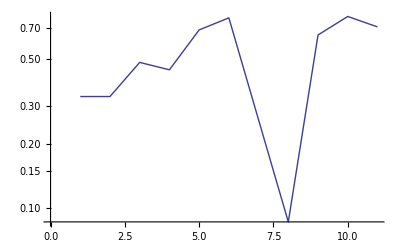

```mathematica
ListLogPlot[Table[values[[i]]/(2 * 3^i), {i,1,Length[values]}], Joined->True]
```

```mathematica
BadTailMod[max_, modulus_]:=BadTailMod[max, modulus]=Module[{pow3,runLength,  x, valueTail, allTwos, result={},hold, start},
pow3=3^(max+1);
runLength=2 * 3^max;
start = 1;
Monitor[
For[x=0, x<runLength,x+=2,
valueTail=PadLeft[IntegerDigits[Mod[start,pow3],3],max+1];
If [!MemberQ[valueTail,2],
hold=Reverse[IntegerDigits[2^x,3]];
AppendTo[result,{x,MyFirst[ Position[hold,2]], Length[hold], valueTail}];
];
start = Mod[start*4, modulus]
],
{x, runLength, modulus}];
result
]
```

```mathematica
TableForm [
Monitor[
Table[
Module[
{bt=Sort[BadTailMod[tailLength, 2^(10*tailLength)],#1[[2]]>#2[[2]]&], highest},
highest = First[bt][[2]];
Select[bt, #[[2]]==highest&]
],
{tailLength,1,20}
], tailLength
],
TableDepth->2
]
```

```mathematica
Range[IntegerPart[Log[3,2^100]+1]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

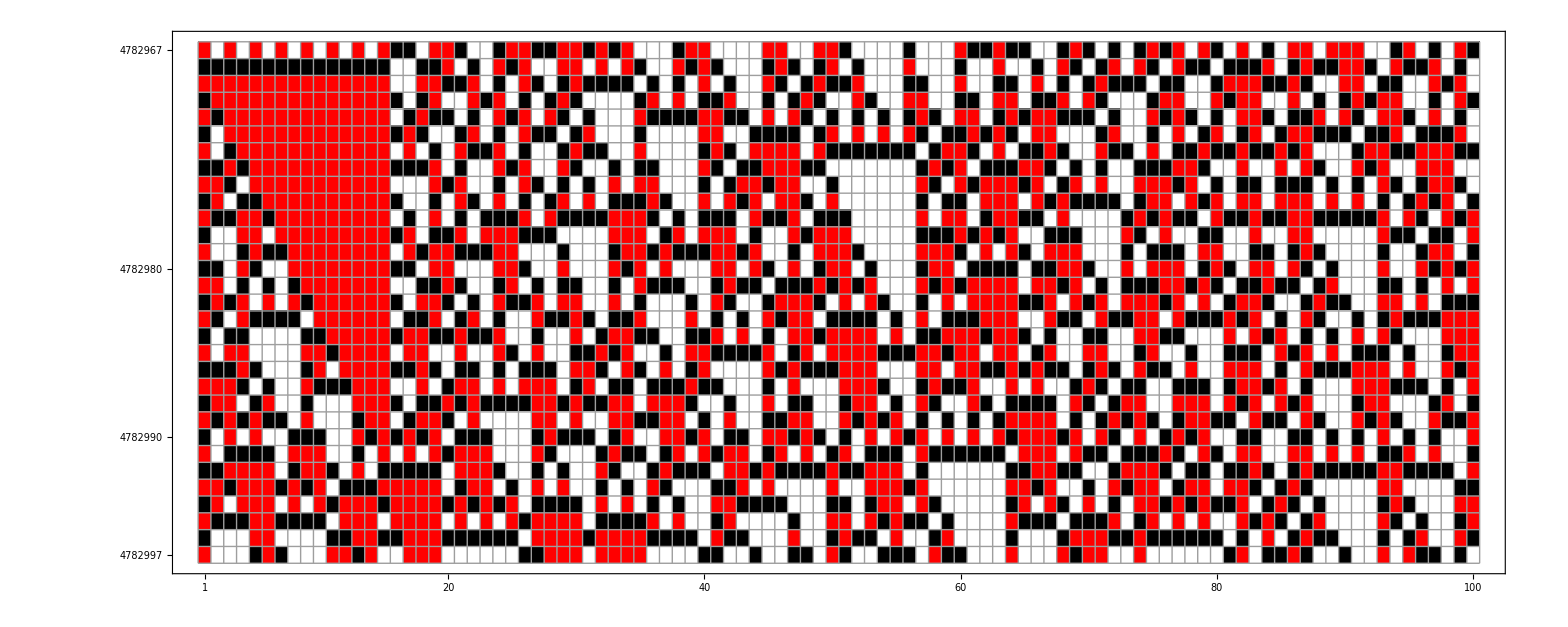

```mathematica
With[
{min=3^14-2,max=3^14+28},
With[
{range = Min[100,IntegerPart[Log[3,2^max]+1]]},
Monitor[
ArrayPlot[
Reverse[Table[PadRight[Reverse[IntegerDigits[2^i,3]],range],{i,min,max}]]
,DataReversed->True,ColorRules->{0->White,1->Black,2->Red},Frame->True, 
FrameTicks->All, Mesh->All,DataRange->{All,{min,max}}, AspectRatio->Automatic]
,i-min]
]
]
```

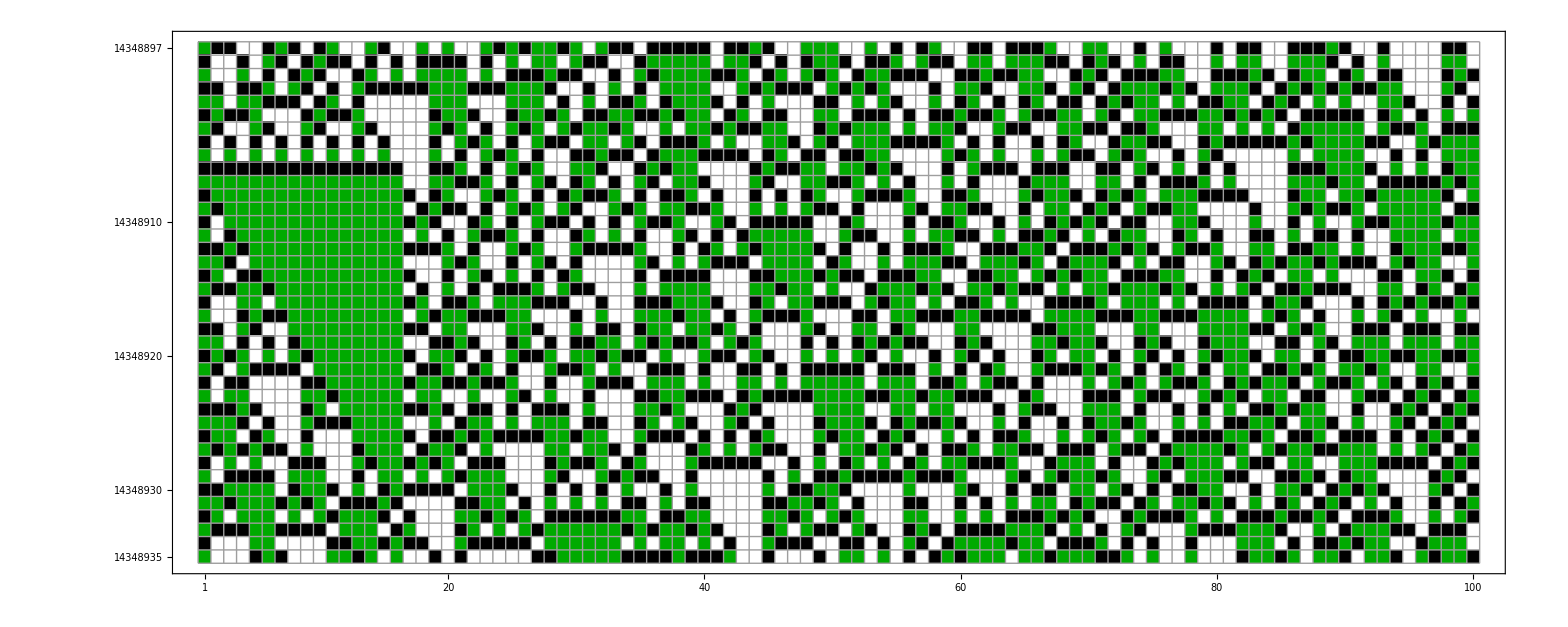

```mathematica
With[
{min=3^15-10,max=3^15+28},
With[
{range = Min[100,IntegerPart[Log[3,2^max]+1]]},
Monitor[
ArrayPlot[
Reverse[Table[PadRight[Reverse[IntegerDigits[2^i,3]],range],{i,min,max}]]
,DataReversed->True,ColorRules->{0->White,1->Black,2->Darker[Green]},Frame->True, 
FrameTicks->All, Mesh->All,DataRange->{All,{min,max}}, AspectRatio->Automatic]
,i-min]
]
]
```

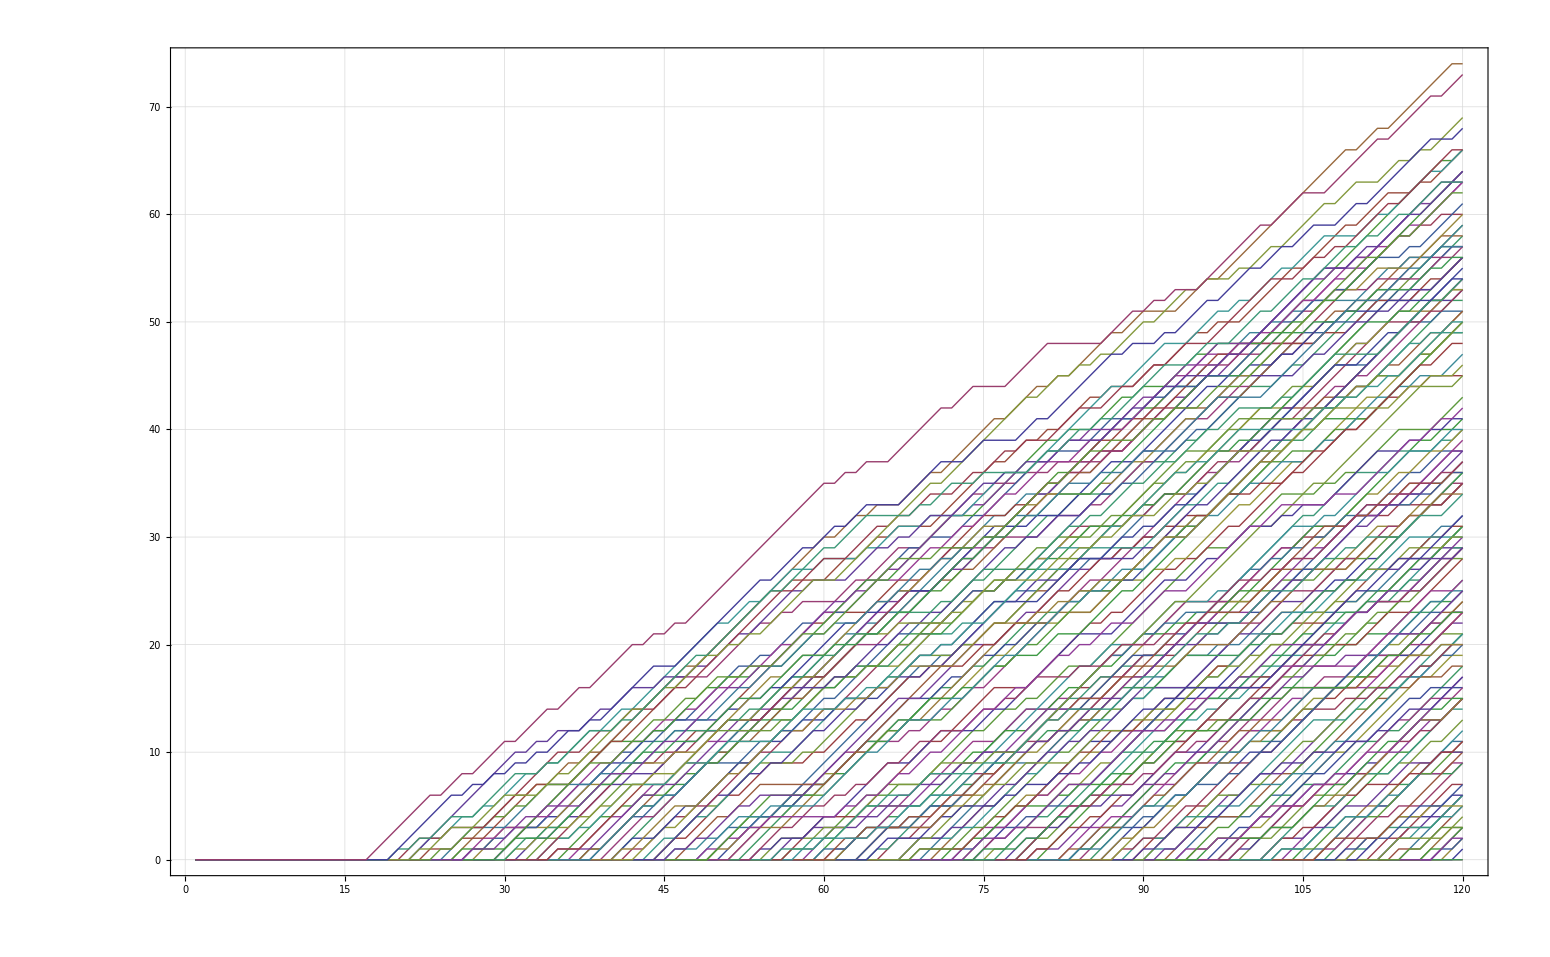

```mathematica
ListLinePlot[
Monitor[

Table[
Tooltip[PadLeft[Accumulate[Reverse[ReplaceAll[IntegerDigits[2^i,3],{0->1,1->1,2->0}]]],120],i]
,{i,0,2*3^4}
],
i],
PlotRange->All,
GridLines->Automatic,
Frame->True,
FrameTicks->Automatic
]
```

```mathematica
Tally[IntegerDigits[2^12888,3]]
```

{{1,2750},{2,2659},{0,2723}}

```mathematica
Tally[IntegerDigits[2^8748,3]]
```

{{1,1840},{2,1927},{0,1753}}

```mathematica
Cases[2,{0->-1,1->1,2->0}]
```

{}

```mathematica
ReplaceAll[{0,2,1},{0->-1,1->1,2->0}]
```

{-1,0,1}

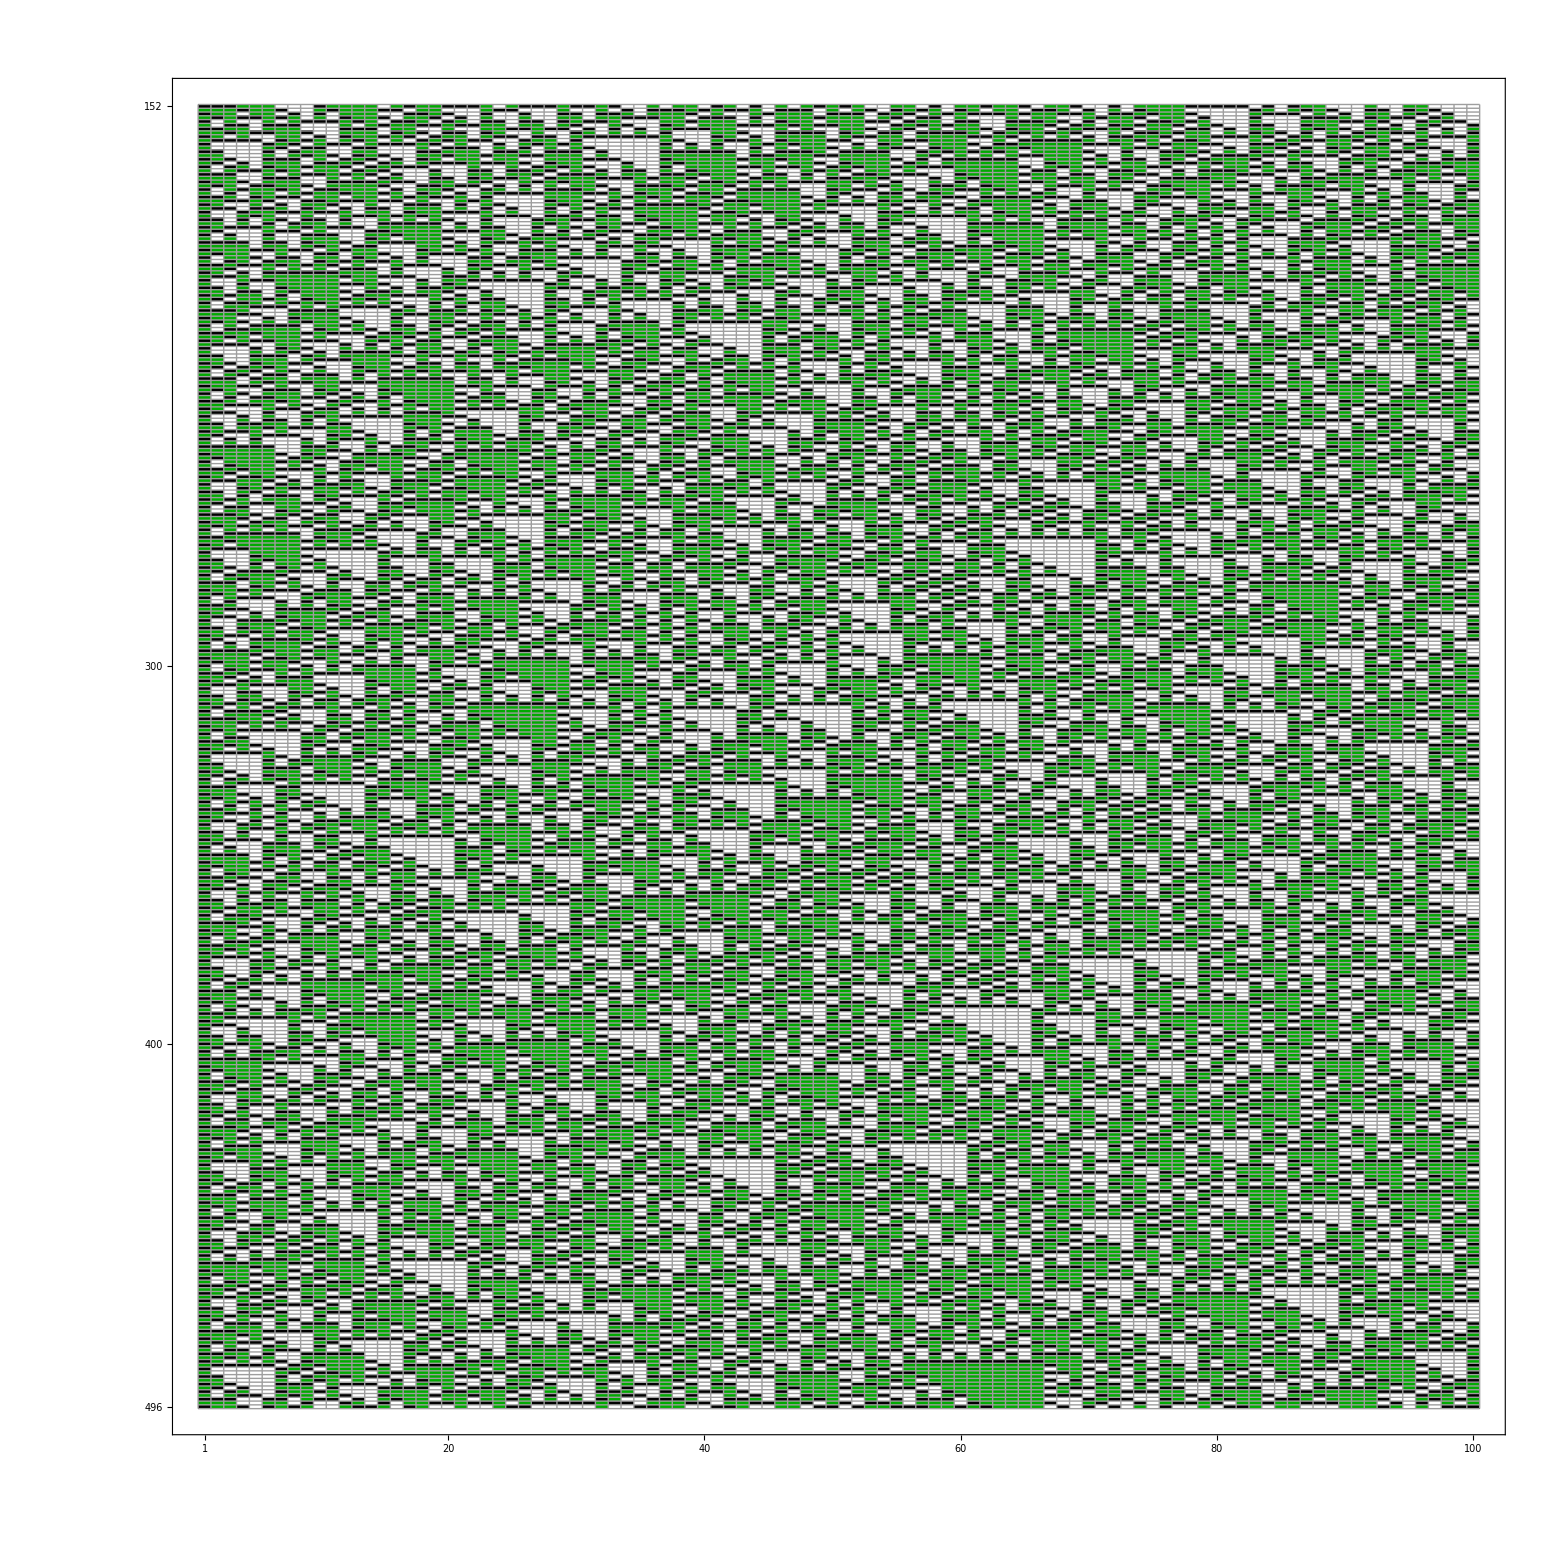

```mathematica
With[
{min=2*3^4-10,max=2*3^5+10},
With[
{range = Min[100,IntegerPart[Log[3,2^max]+1]]},
Monitor[
ArrayPlot[
Reverse[Table[PadRight[Reverse[IntegerDigits[2^i,3]],range],{i,min,max}]]
,DataReversed->True,ColorRules->{0->White,1->Black,2->Darker[Green]},Frame->True, 
FrameTicks->All, Mesh->All,DataRange->{All,{min,max}}, AspectRatio->Automatic]
,i-min]
]
]
```

```mathematica
MyArrayPlot[l_] := ArrayPlot[
List[l]
,DataReversed->True,ColorRules->{0->White,1->Black,2->Darker[Green]}, 
Mesh->All, AspectRatio->Automatic,ImageSize->50]
```

```mathematica
MyArrayPlot[{0,2}]->MyArrayPlot[{1,2}]
```

-Graphics-→-Graphics-

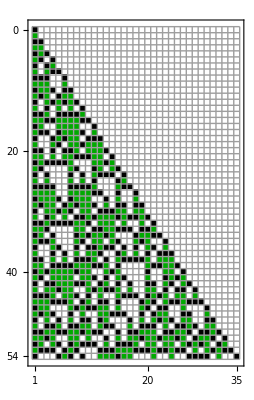

```mathematica
With[
{min=0,max=2*3^3},
With[
{range = Min[100,IntegerPart[Log[3,2^max]+1]]},
Monitor[
ArrayPlot[
Reverse[Table[PadRight[Reverse[IntegerDigits[2^i,3]],range],{i,min,max}]]
,DataReversed->True,ColorRules->{0->White,1->Black,2->Darker[Green]},Frame->True, 
FrameTicks->All, Mesh->All,DataRange->{All,{min,max}}, AspectRatio->Automatic]
,i-min]
]
]
```

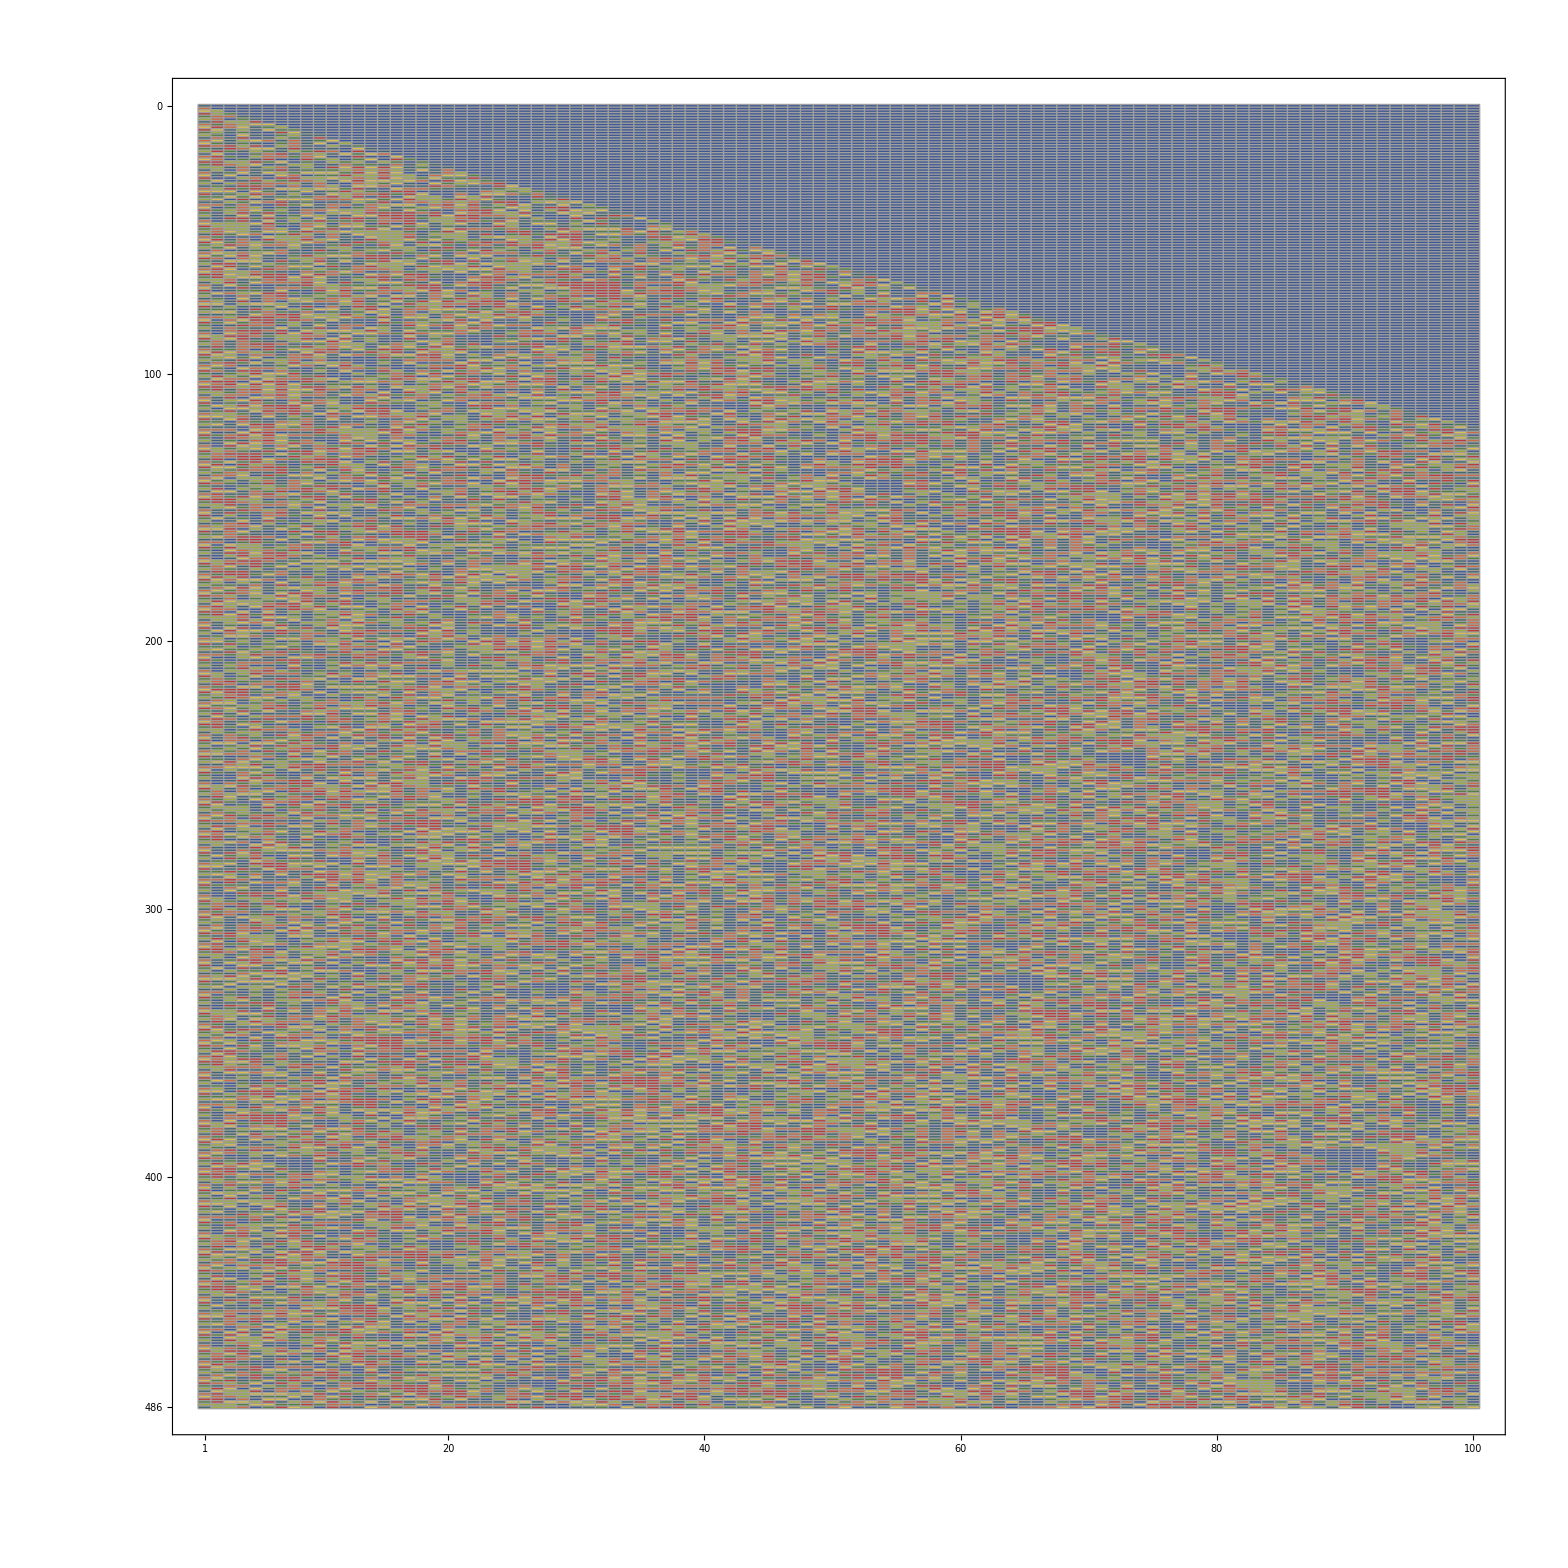

```mathematica
With[
{min=0,max=2*3^5},
With[
{range = Min[100,IntegerPart[Log[3,2^max]+1]]},
Monitor[
ArrayPlot[
Reverse[Table[PadRight[Reverse[IntegerDigits[5^i,7]],range],{i,min,max}]]
,DataReversed->True,Frame->True, ColorFunction->"DarkRainbow",
FrameTicks->All, Mesh->All,DataRange->{All,{min,max}}, AspectRatio->Automatic]
,i-min]
]
]
```